```mathematica
string = "/home/luka/Dropbox/cqp/report/thesis/res/glassgow/C17/Spectrum1540-1550_C17_32.0C.csv"
```

/home/luka/Dropbox/cqp/report/thesis/res/glassgow/C17/Spectrum1540-1550_C17_32.0C.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName[string]]]
```

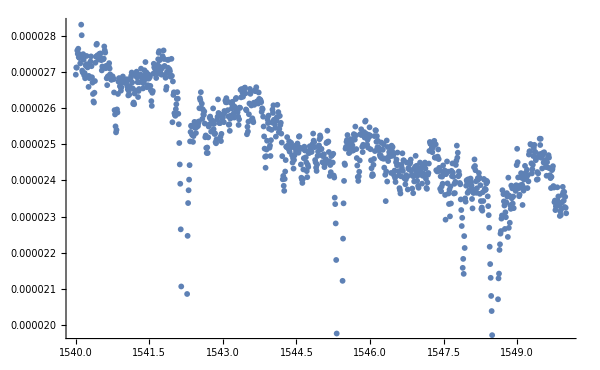

```mathematica
a = Import[string,{"Data",{All},{1,2}}];
ListPlot[a]
```

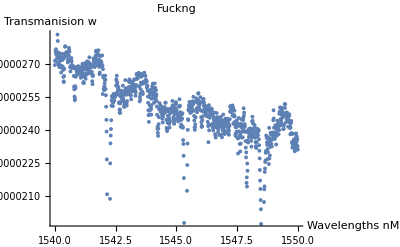

Import::nffil: File not found during Import.

Import::chtype: First argument string is not a valid file, directory, or URL specification. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/Import/chtype",
ButtonNote->"Import::chtype"]

$Failed

```mathematica
Show[%25,AxesLabel->{HoldForm[Wavelengths nM],HoldForm[Transmanision w]},PlotLabel->HoldForm[Fuckng],LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]}]
```